```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\robin\Google Drive\Master's thesis

```mathematica
exportAndDraw[name_,expression_]:=(Export[name,expression];expression)
```

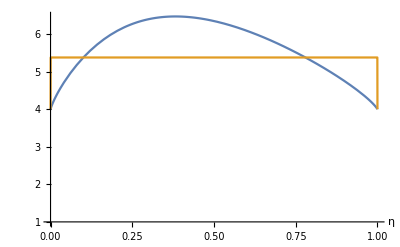

```mathematica
exportAndDraw["binomial-bound.pdf",Plot[{4((1-η)^(1-1/η)/η)^(η/(η+1)),If[η≤0.00001||η≥.99999,4,5.3793]},{η,0,1},PlotRange->{1,4GoldenRatio},AxesLabel->{Style["η",FontFamily->"Cambria Math",FontSize->12]}]]
```

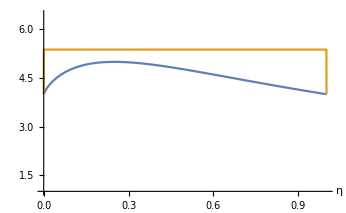

```mathematica
exportAndDraw["spc-bound.pdf",
Plot[{4^(1/(η+1))(η+1)/η^(η/(η+1)),If[η≤0.00001||η≥.99999,4,5.3793]},{η,0,1},PlotRange->{1,4GoldenRatio},AxesLabel->{Style["η",FontFamily->"Cambria Math",FontSize->12]}]]
```

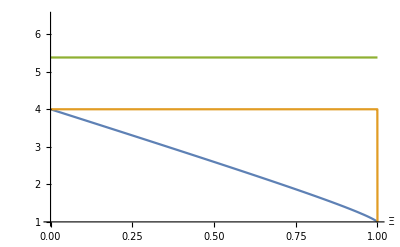

```mathematica
exportAndDraw["convexity-bound.pdf",
Plot[{(1-Ξ)^(Ξ-1)/(2-Ξ)^(Ξ-2),If[Ξ≥.99999,1,4],5.3793},{Ξ,0,1},PlotRange->{1,4GoldenRatio},AxesLabel->{Style["Ξ",Italic,FontFamily->"Cambria Math",FontSize->12]}]]
```